# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Zone1 :prepare, store, detect
Zone2 :prepare, store, detect, logic
Zone3 :prepare, store, detect, logic
Zone4 :remote entangle

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
(* time unit μs *)
T1-><|"Alice"->100, "Bob"->110 |>,
T2-><|"Alice"->40, "Bob"->45|>,
(*fidelity of preparation/initialisation*)
FidInit-><|"Alice"->0.99, "Bob"->0.98|>,
(*fraction of depolarising:dephasing in the initialisation *)
EFInit-><|"Alice"->{1,0}, "Bob"->{1,0}|>,
DurInit-><|"Alice"->2,"Bob"->5|>,
(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual) *)
FidSingleXY-><|"Alice"->0.98, "Bob"->0.99|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{0.2,0.8},"Bob"->{0.1,0.9}|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.97, "Bob"->0.96|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{0,1}|>
};
```

Questlink takes initial indices; thus, passive noise is incorrect. Manually added for every gate?

{{0,{Init_0,SplitZ_(1,2)},{Deph_0[0.0243853],Depol_0[0.014851],Deph_1[0.],Depol_1[0.],Deph_2[0.012345],Depol_2[0.00746262],Deph_3[0.012345],Depol_3[0.00746262],Deph_4[0.0217356],Depol_4[0.0135131],Deph_5[0.0217356],Depol_5[0.0135131],Deph_6[0.0217356],Depol_6[0.0135131],Deph_7[0.0217356],Depol_7[0.0135131]}},{2,{Init_4,SplitZ_(5,6)},{Deph_0[0.0587515],Depol_0[0.0365779],Deph_1[0.],Depol_1[0.],Deph_2[0.0475813],Depol_2[0.0294079],Deph_3[0.0475813],Depol_3[0.0294079],Deph_4[0.0525803],Depol_4[0.0333277],Deph_5[0.0525803],Depol_5[0.0333277],Deph_6[0.0525803],Depol_6[0.0333277],Deph_7[0.0525803],Depol_7[0.0333277]}}}

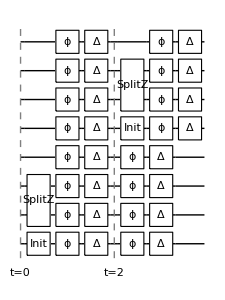

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev=TrappedIonOxford[];
InsertCircuitNoise[{Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[SplitZ, 2,3]["Alice",4],Subscript[SplitZ, 2,3]["Bob",4]},dev,ReplaceAliases->False]
DrawCircuit@%
dev@ShowNodes
```

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 1,2]["Alice",3],Subscript[SplitZ, 1,2]["Bob",2]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[CombZ, 1,2]["Bob",2]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 3,4]["Alice",3]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[CombZ, 2,3]["Bob",2]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 2,3]["Alice",4],Subscript[SplitZ, 2,3]["Bob",4]},dev,ReplaceAliases->False]
DrawCircuit@%
```

InsertCircuitNoise::error: Encountered gate SplitZ_(2,3)[Alice,4] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

DrawCircuit::error: Invalid arguments. See ?DrawCircuit

$Failed